# PRA numerical study: launcher

Keep this notebook in the same folder as Casimir_Optimization_PRA_Mathematica9.m. Start a fresh Mathematica kernel, then evaluate the three input cells in order. SelfTest[] must return True before RunStudy[] is evaluated.

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Casimir_Optimization_PRA_Mathematica9.m"}]]
```

Definitions loaded. Execute SelfTest[] for a quick check and RunStudy[] for the full optimization.

```mathematica
SelfTest[]
```

Self-test Pinf(GaAs, eta=.95) = 3.65028 mPa (reference ~3.65028 mPa)

Self-test generalized PEC plateau = 3.65028 mPa

Self-test Au plateau = 3.52478 mPa (must be below PEC)

Self-test epsilonAu(Eg) = -25.3733+2.31996 ⅈ

Self-test epsilonGaAs-RM(Eg) = 12.9276+0.383292 ⅈ

Self-test epsilonGaAs-RM(i xi1) = 10.9555

Self-test Au finite-gap components = {-0.191801,3.12896,0.000162734,2.93732} mPa

Self-test alternative-GaAs components = {-0.184333,3.24411,-0.00121969,3.05856} mPa

Self-test leakage(b=13.5 um) = 0.00017737 (reference ~1.77e-4)

Self-test equilibrium indicator = 0.001 (reference 1e-3)

SELF-TEST PASSED. It is safe to execute RunStudy[].

True

--- Robust nonequilibrium Casimir optimization (Mathematica 9) ---

Adachi KK completion: eps0Interband = 9.59699, deltaUV = 1.29301

Emission-only thickness at 10^-3 = 10.4476 um

Adopted thickness = 13.5 um

Leakage at adopted b = 0.00017737

Equilibrium coupling indicator = 0.001

Best feasible coarse point: a = 1.35 um, eta = 0.945, J = 2.25608 mPa

OPTIMUM: aL=aR = 1.35122 um; eta = 0.945; b = 13.5 um

Robust bilateral pressure = 2.25684 mPa

Active uncertainty point {delta a [nm], delta eta} = {10.,-0.005}

Nominal {Peq, PPW, PEW, Ptotal} mPa = {-0.18418,3.24196,-0.00121028,3.05657}

Robust cavity excess = 0.181162 mPa

--- PRA extensions: cross-comparison, trade-offs, model checks, and uncertainty audit ---

Gold robust optimum: a = 1.32511 um; J = 2.16428 mPa; robust cavity excess = 0.159991 mPa

Maximum alternative-GaAs-model change at the two validation points = 0.0443564 percent

PRA extension data written to C:\Users\mrkho_000\Desktop\2026_PRA_Casimir_Revision\data_mathematica9_pra

point | aL_um | aR_um | eta | P_reduced_mPa | P_finite_L_mPa | P_finite_R_mPa | P_finite_min_mPa | Delta_min_mPa | Abs_rel_percent
nominal | 1.35122 | 1.35122 | 0.945 | 3.05657 | 3.05655 | 3.05655 | 3.05655 | -0.0000267537 | 0.000875286
active worst case | 1.34122 | 1.36122 | 0.94 | 2.25684 | 2.25681 | 2.2568 | 2.2568 | -0.0000361787 | 0.00160307

Finite-slab validation written to C:\Users\mrkho_000\Desktop\2026_PRA_Casimir_Revision\data_mathematica9_pra\finite_slab_validation.csv

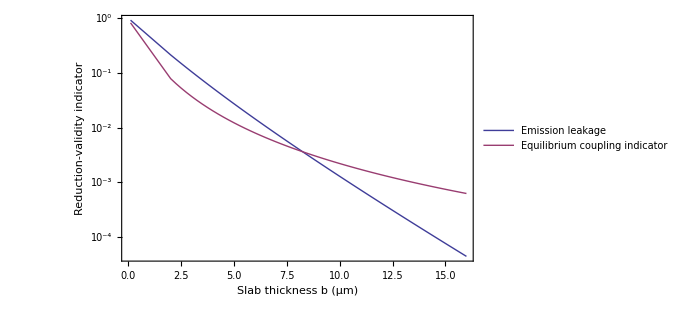

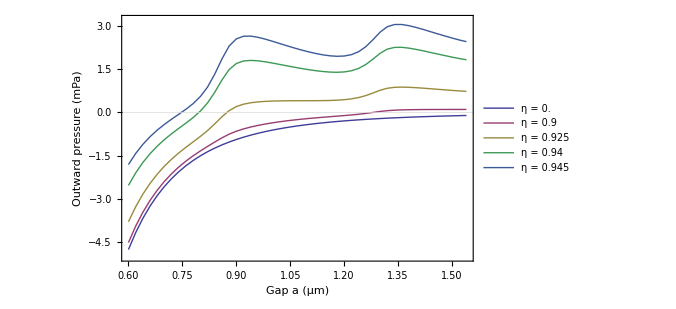

-Graphics-

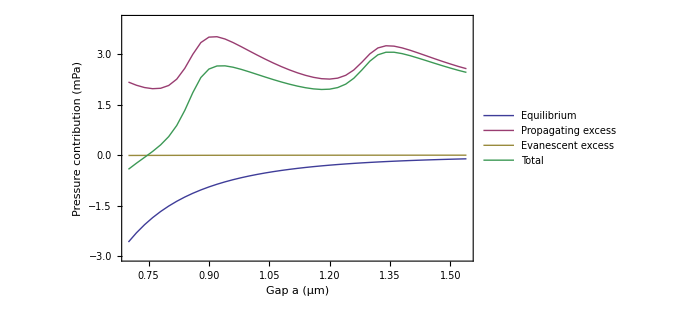

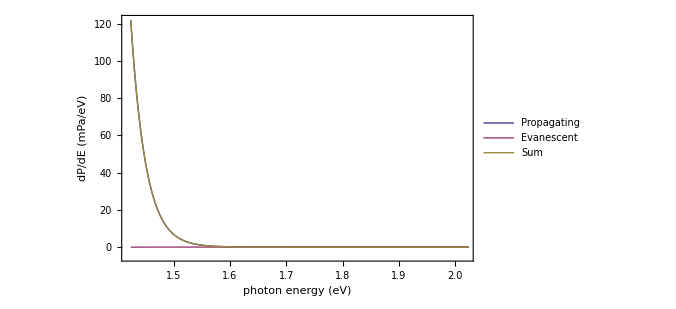

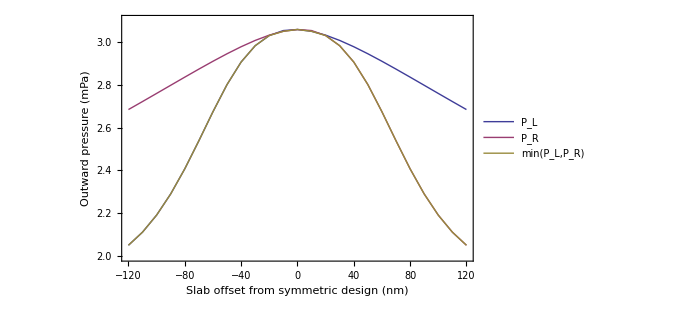

Study complete. CSV data: C:\Users\mrkho_000\Desktop\2026_PRA_Casimir_Revision\data_mathematica9_pra

Figures: C:\Users\mrkho_000\Desktop\2026_PRA_Casimir_Revision\figures_mathematica9_pra

{1.35122×10^-6,0.945,0.0000135,0.00225684,{-0.00010873,0.00256211,-7.77133×10^-7,0.0024526}}

```mathematica
RunStudy[]
```

RunStudy[] writes all manuscript and supplemental CSV tables, including the nominal-robust cross-comparison, robustness trade-off, alternative-GaAs check, PEC-gold comparison, and finite-slab validation, to data_mathematica9_pra. It also displays and exports the six computational plots to figures_mathematica9_pra.